## This notebook contains the code to create analogous graphs to those presented in the paper.

### Case 1: stochastic logistic growth

```mathematica
(*create function to run case study 1 for different r (rDifference) and R (rRatio) values*)
caseStudy1Func[rDifference_,rRatio_,runTime_,n0_]:=Module[
{r=rDifference,
R=rRatio,
(*constants*)
b0,
b1=0,
d0,
d1=0.01,
K,
(*inital conditions*)
t=0,
n=n0,
tstop=runTime,
OutputList,
Event
},

(*solve for b0 and d0*)
b0=r+r/(R-1);
d0=r/(R-1);
(*this would be the equilibrium in a deterministic model*)
K=(b0-d0)/(d1-b1);

(*set up simulation*)
OutputList={{t,n}};
(*"timestepping"*)
While [True,If[t>tstop||n<1,Break[]];
(*define birth, death as the event and give rates*)
Event={(b0+b1*n)*n,(d0+d1*n)*n};
(*find time to next event*)
t+=RandomVariate[ExponentialDistribution[Total[Event]]];
(*determine which event occurred*)
n+= RandomChoice[Event->{1,-1}];
(*record data*)
AppendTo[OutputList,{t,n}];
];
{OutputList,{K}}

]
```

```mathematica
imgsize=350;
fntsize=18;

(*set constants for birth, death functions*)
r=1;
R=1.5;
b0=r+r/(R-1);
b1=0;
d0=r/(R-1);
d1=0.01;
(*this would be the equilibrium in a deterministic model*)
K=(b0-d0)/(d1-b1);

(*display birth and death per capita rates as a function of N for two values of R*)

(*R=1.5*)
p1=Plot[b0+b1*x, {x,0,1.5*K},
 PlotRange->{Automatic,{0,1.2*b0}},
PlotStyle->{Darker[Green]}, 
PlotLabel->"(a) Birth and death rates",
Frame->{True,True,False, False},
FrameLabel->{"N","rate"},
FrameTicks->{{40,80,120},Automatic},
 PlotLabels->"birth, R=1.5",
 AspectRatio->1,
BaseStyle->FontSize->fntsize,
ImageSize->imgsize,
 ImageMargins->{{0,0},{0,200}}
];
p2=Plot[d0+d1*x, {x,0,1.5*K},
 PlotStyle->{Darker[Red]},
PlotLabels->"death, R=1.5", 
AspectRatio->1];

(*R=5*)
R=5;
b0=r+r/(R-1);
b1=0;
d0=r/(R-1);
p3=Plot[b0+b1*x, {x,0,1.5*K}, 
PlotStyle->{Darker[Green],Dashed},
PlotLabels->"birth, R=5",
 AspectRatio->1];
p4=Plot[d0+d1*x, {x,0,1.5*K}, 
PlotStyle->{Darker[Red],Dashed},
PlotLabels->"death, R=5", 
AspectRatio->1];
plt1=Show[p1,p2,p3,p4];
```

```mathematica
(*simulate*)

(*set up simulation conditions*)
tstop=2000;
rLittle=1;
graphMax=100;

(*run for R=1.5*)
OutputList=caseStudy1Func[rDifference=rLittle,rRatio=1.5,runTime=tstop,n0=10];
K=Flatten[OutputList[[2]]][[1]]
OutputList=OutputList[[1]];
OutputList1=OutputList;

(*run for R=5*)
OutputList=caseStudy1Func[rDifference=rLittle,rRatio=5,runTime=tstop,n0=10];
K=Flatten[OutputList[[2]]][[1]]
OutputList=OutputList[[1]];
OutputList2=OutputList;
```

100.

100.

```mathematica
(*make graphs*)
lp1=ListLinePlot[Select[OutputList1,#[[1]]<graphMax&],
PlotRange->{{0,graphMax},{0,2*K}},
PlotLabel->"(b) Population dynamics, R= 1.5",
Frame->{True,True,False, False},FrameLabel->{"Time","N"},
PlotStyle->Darker[Blue],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];
histData=Select[OutputList1,#[[1]]>(tstop/2)&];

h1=Histogram[histData[[All,2]],{2},"Probability",
PlotRange->{{0,0.15},{0,2*K}},
BarOrigin->Left, 
ChartStyle->Darker[Blue],
ChartBaseStyle->EdgeForm[None],
PlotLabel->"(c) Frequency distribution",
Frame->{True,True,False, False},
FrameLabel->{"Frequency","N"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];

lp2=ListLinePlot[Select[OutputList2,#[[1]]<graphMax&],
PlotRange->{{0,graphMax},{0,2*K}},
PlotLabel->"(d) Population dynamics, R= 5",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->Darker[Orange],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];

histData=Select[OutputList2,#[[1]]>(tstop/2)&];

h2=Histogram[histData[[All,2]],{2},"Probability",
PlotRange->{{0,0.15},{0,2*K}},
BarOrigin->Left, 
ChartStyle->Darker[Orange],
ChartBaseStyle->EdgeForm[None],
PlotLabel->"(e) Frequency distribution",
Frame->{True,True,False, False},
FrameLabel->{"Frequency","N"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];
```

```mathematica
(*plot combined graph*)
case1=Grid[{{plt1,lp1,h1},{SpanFromAbove,lp2,h2}}]
(*Export["FILEPATH/case1.png",case1]*)
```

### Case 2

```mathematica
(*set up*)
fntsize=18;
imgsize=350;
b1=0
d0=1;
d1=0.01;
(*define rule to translate trait into demographic rates (birth rate variaiton)*)
traitToRateFunc[phenotype_,optimum_,spread_,maxval_,minval_]:=(maxval-minval)*ⅇ^(-(phenotype-optimum)^2/(2*spread^2))+minval;

(*create function to run case study 2 for different w (genetic weight) values*)
caseStudy2Func[geneticWeight_,runTime_, n0_]:= Module[
{b0=3, (*optimal b0*)
b1=b1,
d0=d0,
d1=d1,
K=(b0-d0)/(d1-b1),
(* note the variation in the population will be in the birth term i.e, b0*)

(*initialize starting trait distributions*)
ϕMeanOriginal=-3/geneticWeight,
ϕDevOriginal=1,

σMutation=0.1,

environmentalMean=0,
σEnvironmental=3,

heritabilityWeight=geneticWeight,

σTranslationSpread=2,

n=n0,
t=0,
tstop=runTime,

αOptimal,
bOptimal,

ϕ,
α,
bVec,
Event,
change,
newϕ,
newα,
new,
dead,

(*outputs*)
bMean,
bSTDEV,
ϕMean,
ϕSTDEV,
αMean,
αSTDEV,
OutputList

},
αOptimal=0;
bOptimal=b0;
(*genotype*)
ϕ=RandomVariate[NormalDistribution[ϕMeanOriginal,ϕDevOriginal],n0];

(*"phenotype" that incorporates environmental effects*)
α=heritabilityWeight*ϕ + (1-heritabilityWeight)*RandomVariate[NormalDistribution[environmentalMean,σEnvironmental],n0];

(*translate phenotype to birthrate*)

bVec=traitToRateFunc[#,αOptimal,σTranslationSpread,bOptimal,d0]&/@α;

n=n0;
(*what do we want to record*)
bMean=Mean[bVec];
bSTDEV=StandardDeviation[bVec];
ϕMean=Mean[ϕ];
ϕSTDEV=StandardDeviation[ϕ];
αMean=Mean[α];
αSTDEV=StandardDeviation[α];

OutputList={{t,n,bMean,bSTDEV,ϕMean,ϕSTDEV,αMean,αSTDEV}};

While [True,If[t>tstop||n<1,Break[]];
Event=Append[bVec,(d0+d1*n)*n];
t+=RandomVariate[ExponentialDistribution[Total[Event]]];
change= RandomChoice[Event->Append[Range[n],-1]];
If[change>0,
newϕ=RandomVariate[NormalDistribution[ϕ[[change]],σMutation]];
newα=heritabilityWeight*newϕ+(1-heritabilityWeight)*RandomVariate[NormalDistribution[environmentalMean,σEnvironmental]];
new=traitToRateFunc[newα,αOptimal,σTranslationSpread,bOptimal,d0];
AppendTo[ϕ,newϕ];
AppendTo[α,newα];
AppendTo[bVec,new],
dead=RandomChoice[Range[n]];bVec=Delete[bVec,dead];
ϕ=Delete[ϕ,dead];
α=Delete[α,dead]
];


n=Length[bVec];
bMean=Mean[bVec];
bSTDEV=StandardDeviation[bVec];
ϕMean=Mean[ϕ];
ϕSTDEV=StandardDeviation[ϕ];
αMean=Mean[α];
αSTDEV=StandardDeviation[α];

AppendTo[OutputList,{t,n,bMean,bSTDEV,ϕMean,ϕSTDEV,αMean,αSTDEV}];

];
{OutputList, bVec, ϕ, α}
]
```

0

```mathematica
(*run simulations*)
tstop=200;

(*100% genetic*)
w=1;
OutputList= caseStudy2Func[geneticWeight=w,runTime=tstop,n0=25];
bVec1= OutputList[[2]];
ϕ1= OutputList[[3]];
Tvec1= OutputList[[4]];
OutputList1= OutputList[[1]];

(*50% genetic*)
w=0.5;
OutputList= caseStudy2Func[geneticWeight=w,runTime=tstop,n0=25];
bVec2= OutputList[[2]];
ϕ2= OutputList[[3]];
Tvec2= OutputList[[4]];
OutputList2= OutputList[[1]];
```

```mathematica
(*make figures*)
in1=Plot[genotypeToPhenotypeFunc[x,0,3,3,1],{x,-10,10},
PlotRange->{{-10,10},{0,3}} ,
PlotStyle->Darker[Green],
PlotLabel->"(b) Trait to birth rate mapping",
Frame->{True,True,False, False},
FrameLabel->{"Trait value (T)","Individual birth rate"},
Epilog->{Black,Line[{{1.8,0},{1.8,genotypeToPhenotypeFunc[1.8,0,3,3,1]}}]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];

a=RandomVariate[NormalDistribution[1.75,0.2],20];
br=Map[genotypeToPhenotypeFunc[#,0,3,3,1]&,a];

plt1=Show[
Plot[br,{x,0,250},
PlotStyle->{{Darker[Green],Opacity[0.3]}},
PlotRange->{{0,250},{0,4}} ,
PlotLabel->"(a) Birth and death rates per individual",
Frame->{True,True,False, False},
FrameLabel->{"N","Per capita event rates"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[{(d0+d1*n)},{n,0,250},
 PlotStyle->Darker[Red]],
Plot[genotypeToPhenotypeFunc[1.8,0,3,3,1],{x,0,250},
PlotStyle->Black]
];
```

```mathematica
(*population dynamocs w=1*)
p1=ListLinePlot[OutputList1[[;;,{1,2}]],
PlotRange->{{0,tstop},{0,250}},
PlotLabel->"(c) Population dynamics with w=1",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->Darker[Blue],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
(*phenotype*)
p2=ListLinePlot[OutputList1[[;;,{1,7}]],
PlotRange->{{0,tstop},{-6,3}},
PlotLabel->"(d) Mean trait shifts with w=1",
Frame->{True,True,False, False},
FrameLabel->{"Time","Trait value (T)"},
PlotStyle->Darker[Blue],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
```

```mathematica
(*population dynamocs w=0.5*)
p3=ListLinePlot[OutputList2[[;;,{1,2}]],
PlotRange->{{0,tstop},{0,250}},
PlotLabel->"(e) Population dynamics with w=1",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->Darker[Orange],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
(*phenotype*)
p4=ListLinePlot[OutputList2[[;;,{1,7}]],
PlotRange->{{0,tstop},{-6,3}},
PlotLabel->"(f) Mean trait shifts with w=1",
Frame->{True,True,False, False},
FrameLabel->{"Time","Trait value (T)"},
PlotStyle->Darker[Orange],
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
```

```mathematica
case2=Grid[{{plt1,p1,p2},{in1,p3,p4}}]
(*Export["FILEPATH/case2.png",case2]*)
```

-Graphics-

## Case 3

```mathematica
b0=0.8;
d0=0.25;
d1=0.01;
K=(b0-d0)/(d1);

(*functions*)
(*time dependent birth function*)
birthRateFunc[time_,n_,β_,α_]:=Module[{b0=b0},(b0+β*Sin[α*time])*n]
(*time independent death function*)
deathRateFunc[n_]:=Module[{d0=d0,d1=d1},(d0+d1*n)*n]

λFunc[time_,n_,β_,α_]:=birthRateFunc[time,n,β,α]+deathRateFunc[n]

timestepBackcalculateFunc[n_,t_,rnum_,precision_,β_,α_]:=Module[
{τ,
cdfInterval,
cdf,
tIntegral,
bIntegralSegment,
dIntegralSegment,
λIntegralSegment,
λTotal,
stepCount,
Event,
error,
output},

τ=rnum;
tIntegral=t;
cdf=0;
error=Abs[cdf-τ];

stepCount=0;

cdfInterval=0.1;

λTotal=0;

While[error>precision||stepCount<1,
While[cdf<τ,
bIntegralSegment=cdfInterval*1/2(birthRateFunc[tIntegral,n,β,α]+birthRateFunc[(tIntegral+cdfInterval),n,β,α]);
dIntegralSegment=cdfInterval*1/2(deathRateFunc[n]+deathRateFunc[n]);
λIntegralSegment=bIntegralSegment+dIntegralSegment;
λTotal+=λIntegralSegment;
cdf=1-Exp[-λTotal];
tIntegral+=cdfInterval;

stepCount+=1
];
(*retract the overstepping step*)
stepCount-=1;
tIntegral-=cdfInterval;
λTotal-=λIntegralSegment;
cdf=1-Exp[-λTotal];

error=Abs[cdf-τ];
cdfInterval=cdfInterval*0.1
];
output=tIntegral;
output
]

caseStudy3Func[amplitude_,frequency_,runTime_,n0_]:=Module[
{
b0=b0,
β=amplitude,
α=frequency,

d0=d0,
d1=d1,
(*inital conditions*)
t,
n,
tstop=runTime,
OutputList,
Event,
τ
},
t=0;
n=n0;
OutputList={{t,n}};
While [True,If[t>tstop||n<1,Break[]];
τ=RandomReal[];
t=timestepBackcalculateFunc[n,t,τ,0.0001,β,α];
Event={birthRateFunc[t,n,β,α],deathRateFunc[n]};
n+= RandomChoice[Event->{1,-1}];
AppendTo[OutputList,{t,n}];
];
OutputList
]
```

```mathematica
imgsize=350;
fntsize=18;
K=(b0-d0)/(d1);

β=0.35;
α=0.1;
plt1=Show[
Plot[{b0+β},{x,0,2*K},
PlotStyle->{Darker[Green]},
PlotRange->{{0,2*K},{0,1.2*(b0+β)}} ,
PlotLabel->"(a) Birth and death rates",
Frame->{True,True,False, False},
FrameLabel->{"N","Event rates"},
PlotLabels->"max birth",
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[{b0-β},{x,0,2*K},
PlotStyle->{Dashed,Darker[Green]},
PlotLabels->"min birth"],
Plot[{(d0+d1*n)},{n,0,2*K},
PlotStyle->{Darker[Red]},
PlotLabels->"death"]
];

plt2=Plot[birthRateFunc[t,1,β,α],{t,0,200},
PlotRange->{{0,200},{0,1.2*(b0+β)}} ,PlotStyle->{Darker[Green]},PlotLabel->"(b) Example sequence of \n birth rates over time",
Frame->{True,True,False, False},
FrameLabel->{"t","Individual birth rate"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];
```

```mathematica
tstop=300;
β=0;
α=0.1;
n0=10;

odesoln0=NDSolve[{y'[x]==(b0+β*Sin[α*x])*y[x]-(d0+d1*y[x])*y[x],y[0]==n0},y,{x,0,tstop}];
OutputList0=caseStudy3Func[amplitude=β,frequency=α,runTime=tstop,n0=n0];
```

```mathematica
β=0.1;
odesoln01=NDSolve[{y'[x]==(b0+β*Sin[α*x])*y[x]-(d0+d1*y[x])*y[x],y[0]==n0},y,{x,0,tstop}];
OutputList01=caseStudy3Func[amplitude=β,frequency=α,runTime=tstop,n0=n0];
```

```mathematica
β=0.5;
odesoln05=NDSolve[{y'[x]==(b0+β*Sin[α*x])*y[x]-(d0+d1*y[x])*y[x],y[0]==n0},y,{x,0,tstop}];
OutputList05=caseStudy3Func[amplitude=β,frequency=α,runTime=tstop,n0=n0];
```

```mathematica
β=0.8;
odesoln08=NDSolve[{y'[x]==(b0+β*Sin[α*x])*y[x]-(d0+d1*y[x])*y[x],y[0]==n0},y,{x,0,tstop}];
OutputList08=caseStudy3Func[amplitude=β,frequency=α,runTime=tstop,n0=100];
```

```mathematica
p1=Show[ListLinePlot[OutputList0,
PlotRange->{{0,tstop},{0,3*K}},
PlotLabel->"(c) Population dynamics with β=0",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->{Darker[Blue],Directive[Opacity[0.75]]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[Evaluate[y[x]/. odesoln0],{x,0,tstop},PlotRange->All,PlotStyle->{Darker[Blue,0.8],Dashed}]
];
p2=Show[ListLinePlot[OutputList01,
PlotRange->{{0,tstop},{0,3*K}},
PlotLabel->"(d) Population dynamics with β=0.1",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->{Darker[Orange],Directive[Opacity[0.75]]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[Evaluate[y[x]/. odesoln01],{x,0,tstop},PlotRange->All,PlotStyle->{Darker[Orange,0.8],Dashed}]
];
p3=Show[ListLinePlot[OutputList05,
PlotRange->{{0,tstop},{0,3*K}},
PlotLabel->"(e) Population dynamics with β=0.5",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->{Darker[Purple],Directive[Opacity[0.75]]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[Evaluate[y[x]/. odesoln05],{x,0,tstop},
PlotRange->All,
PlotStyle->{Darker[Purple,0.8],Dashed}]
];
p4=Show[ListLinePlot[OutputList08,
PlotRange->{{0,tstop},{0,3*K}},
PlotLabel->"(f) Population dynamics with β=0.8",
Frame->{True,True,False, False},
FrameLabel->{"Time","N"},
PlotStyle->{Darker[Gray],Directive[Opacity[0.75]]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[Evaluate[y[x]/. odesoln08],{x,0,tstop},
PlotRange->All,
PlotStyle->{Darker[Gray,0.8],Dashed}]
];
```

```mathematica
case3=Grid[{{plt1,p1,p2},{plt2,p3,p4}}]
(*Export["FILEPATH/case3.png",case3]*)
```

-Graphics-

## Case 4

```mathematica
(*barea=5,
midpoint=7.5,
width=5*)


(*we want to preserve K?*)

(*Lets Say K=100
then we know at "equilibrium" per capita death rate d_eq=d0+100d1
	and we need the per capita birth rate to be equal: b_eq=deq=d0+100d1 (since this is not density dependent); Assuming all individuals are equal in birth rate
Average lifetime is 1/deq
So if birth is constant over life then expected biths per individual is deq/deq= which makes total sense!
But now if we have births only over some fraction of the lifespan is it sufficient to simply have the birth rate be deq* deq/REPRODUCTIVE SPAN?
		
*)

caseStudy4Func1[Kapprox_,maturation_,timesteps_,n0_,A0_]:=Module[
{
(*constants*)
d0=0.01,
d1=0.001,
deq,
beq,
b0, (*birth rate of adults*)
α1,
α2,
(*set up model start conditions*)
t=0,
tmax=timesteps,
timestepPrecision=4,
U,
tNext,
eventVec,
event,
outcome,
ϕ,
modelOutput,
b,
d,
timestepCalculationFunc,
n
},
(*constants*)
deq=d0+Kapprox*d1;
α1=maturation;
α2=1/deq;
beq=deq;
b0=beq/(Exp[-deq*α1]-Exp[-deq*α2]); (*birth rate of adults*)

(*start with: vector of inidvidual birth times to track age*)
(*initialize starting population with negative birth times so individuals have positive age at the start t=0*)
ϕ=RandomReal[{-A0,0},n0];

(*store model outputs*)
modelOutput={};

(*function definitions for birth, death*)

b[α_]:= Piecewise[{{0,α<α1},{b0,α1<=α<α2},{0,α2<=α}}];
d[α_,n_]:=d0+d1*n;
timestepCalculationFunc[age_,rval_,decimalPrecision_]:=Module[
{last,
runarea,
cont1=True,
cont2=True,
error=10^(-decimalPrecision),
τ=0,
dτ=0.1,
N=Length[age]},
runarea=ConstantArray[0,N];
While[
cont1,
While[
cont2,
(*this loop continues until the integral exceeds rval*)
last=runarea;

(*Take integral for each individual using trapezoid method*)
Do[
runarea[[j]]+=((b[age[[j]]+τ]+b[age[[j]]+τ+dτ])/2)dτ+((d[age[[j]]+τ,N]+d[age[[j]]+τ+dτ,N])/2)dτ,
{j,1,N}
];
If[rval<(1-Exp[-Total[runarea]]),
runarea=last;
dτ=0.1*dτ;
Break[]];
τ+=dτ
];
If[(rval-(1-Exp[-Total[runarea]]))<error,
If[Total[runarea]>0,Break[]]
]
];
τ
];




(*Model loop*)

While[
t<tmax,
n=Length[ϕ];
U=RandomReal[];
tNext=timestepCalculationFunc[t-ϕ,U,timestepPrecision];
eventVec=Join[Map[d[#,n]&,(t-ϕ)],Map[b[#]&,(t-ϕ)]];
event=RandomChoice[eventVec->Range[1,2n]];

(*advance time*)
t+=tNext;
(*update system state*)
If[event<=n,ϕ=Drop[ϕ,{event}],AppendTo[ϕ,t]];

(*record data*)
AppendTo[modelOutput,{t,Length[ϕ],Mean[t-ϕ]}];

(*stop condition*)
If[Length[ϕ]==0,Break[]]
];
modelOutput
]
```

```mathematica
imgsize=350;
fntsize=18;

maturation=1;
K=100;
d0=0.01;
d1=0.001;
deq=d0+K*d1;
α1=maturation;
α2=1/deq;
beq=deq;
b0=beq/(Exp[-deq*α1]-Exp[-deq*α2]);

b[α_]:= Piecewise[{{0,α<α1},{b0,α1<=α<α2},{0,α2<=α}}]

d[α_,n_]:=d0+d1*n;

plt2=
Plot[{b[x],d[x,100]},{x,0,15},
PlotRange->{{0,1.2*α2},{0,1.2*b0}},
Filling->Axis,
PlotLabel->"(b)Rates across age",
Frame->{True,True,False, False},
FrameLabel->{"age","event rates"},
PlotLabels->{"birth", "death"},
PlotStyle->{Darker[Green,0.6],Darker[Red,0.6]},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];

plt1=Show[
Plot[{b0},{x,0,1.5*K},
PlotStyle->{Darker[Green]},
PlotRange->{{0,1.5*K},{0,1.2*b0}} ,
PlotLabels->"adult birth",
PlotLabel->"(a) Birth and death rates",
Frame->{True,True,False, False},
FrameTicks->{{40,80,120},Automatic},
FrameLabel->{"N","event rates"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
Plot[{0},{x,0,1.5*K},
PlotStyle->{Dashed,Darker[Green],Thickness[0.012]},
PlotLabels->"juvenile birth"],
Plot[{(d0+d1*n)},{n,0,1.5*K},
PlotStyle->{Darker[Red]},
PlotLabels->"death rate"]
];
```

```mathematica
tmax=200;
K=100;
n0=50;(*starting population*)
d0=0.01;
d1=0.001;
deq=d0+K*d1;
A0=1/deq;


M1=1;
α1=M1;
α2=1/deq;
beq=deq;
b0=beq/(Exp[-deq*α1]-Exp[-deq*α2]);
(*function definitions for birth, death*)
b[α_]:= Piecewise[{{0,α<α1},{b0,α1<=α<α2},{0,α2<=α}}];
d[α_,n_]:=d0+d1*n;

(*model*)
modelOut1=caseStudy4Func1[Kapprox=K,maturation=M1,timesteps=tmax,n0=n0,A0=A0];


M1=8.5
α1=M1;
α2=1/deq;
beq=deq;
b0=beq/(Exp[-deq*α1]-Exp[-deq*α2]);
(*function definitions for birth, death*)
b[α_]:= Piecewise[{{0,α<α1},{b0,α1<=α<α2},{0,α2<=α}}];
d[α_,n_]:=d0+d1*n;

(*model*)
modelOut85=caseStudy4Func1[Kapprox=K,maturation=M1,timesteps=tmax,n0=n0,A0=A0];
```

8.5

```mathematica
p1=ListPlot[modelOut1[[1;;,{1,2}]],
Joined->True,
PlotStyle->Darker[Blue],
PlotLabel->"(c) Population size \n maturity at age 1",
Frame->{True,True,False, False},
FrameLabel->{"t","N"},
PlotRange->{Automatic,{1,1.5*K}},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];

p2=ListPlot[modelOut1[[1;;,{1,3}]],
Joined->True,
PlotStyle->Darker[Blue],
PlotLabel->"(d) Average age\n maturity at age 1",
Frame->{True,True,False, False},
FrameLabel->{"t","age"},
PlotRange->{Automatic,2*α2},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
```

```mathematica
p3=ListPlot[modelOut85[[1;;,{1,2}]],
Joined->True,
PlotStyle->Darker[Orange],
PlotLabel->"(e) Population size \n maturity at age 8.5 ",
Frame->{True,True,False, False},
FrameLabel->{"t","N"},
PlotRange->{Automatic,{1,1.5*K}},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];

p4=ListPlot[modelOut85[[1;;,{1,3}]],
Joined->True,
PlotStyle->Darker[Orange],
PlotLabel->"(f) Average age \n maturity at age 8.5",
Frame->{True,True,False, False},
FrameLabel->{"t","age"},
PlotRange->{Automatic,2*α2},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize
];
```

```mathematica
case4=Grid[{{plt1,p1,p2},{plt2,p3,p4}}]
(*Export["FILEPATH/case4.png",case4]*)
```

-Graphics-

/Users/mishakummel/Documents/2023-24 Academic Year/rotation/review paper/paper figures/case4.png

## Appendix A: An algorithm for solving the time-steps of non-homogeneous processes (time-varying environments)

```mathematica
(*create an example rate function that varies in time*)
b0=1;
b1=1;
a0=10;
rateFunc[x_,t_]:=x*(b0-b1*Cos[a0*t]);
(*actual CDF of the rate function for comparison with algorithm*)
cdfActualFunc[z_]:=1-Exp[-Integrate[x0*(b0-b1*Cos[a0*x]),{x,0,z}]];
```

```mathematica
(*Example of timestepping algorithm based on Legault and Melbourne*)

(*let's say we chose the random value 0.75 from the uniform distribution*)
rval=0.75;

(*set up variables to track and report each step*)
τList={0};
areaList={{0,0}};
cdfList1={{0,0}};
cdfList2={};
cdfList3={};
cont1=True;

(*initalize algorithm*)
t0=0;
t=t0;
runarea=0;
x0=1;

error=0.001;
τ=0;
dτ=0.1;
(*iterate until rval is reached by CDF*)
While[cont1,
While[cont1,(*for a given increment dτ, iterate until rval is passed, then go back one increment dτ, decrease the size of dτ, and repeat until the cdf of τ is within the error margin of rval and CDF (τ)>0 (i.e., nonzero amount of time has elapsed) *)
last=runarea;
runarea+=dτ*((rateFunc[x0,t+τ]+rateFunc[x0,t+τ+dτ])/2);
If[rval<(1-Exp[-Total[runarea]]),
runarea=last;
dτ=0.1*dτ;
Break[]];
τ+=dτ;
AppendTo[τList,τ];
AppendTo[areaList,{τ,runarea}];
If[dτ==0.1,AppendTo[cdfList1,{τ,1-Exp[-runarea]}]];
If[dτ==0.01,AppendTo[cdfList2,{τ,1-Exp[-runarea]}]];
If[dτ==0.001,AppendTo[cdfList3,{τ,1-Exp[-runarea]}]]

];
If[(rval-(1-Exp[-runarea]))<error,
If[Total[runarea]>0,Break[]]
]
]
```

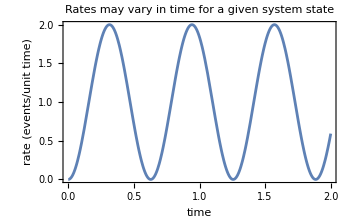

```mathematica
imgsize=500;
fntsize=18;

Plot[rateFunc[1,t],{t,0,2},
PlotLabel->"Rates may vary in time\n for a given system state",
Frame->{True,True,False, False},
FrameLabel->{"time","rate (events/unit time)"},
ImageSize->350,
BaseStyle->FontSize->fntsize,
ImageSize->imgsize]
```

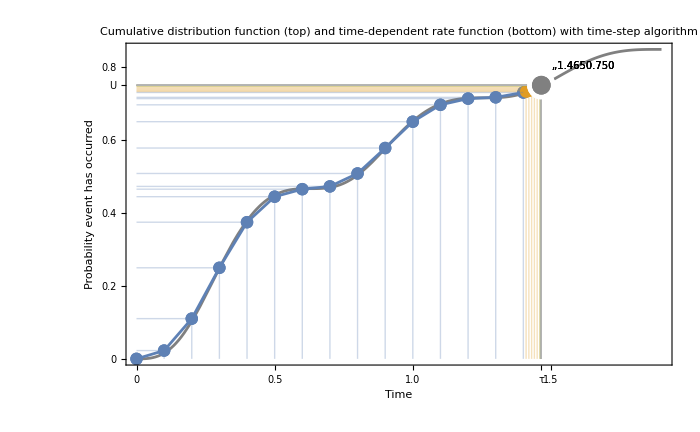

```mathematica
limit=1.9;
plottemp=Plot[cdfActualFunc[y],{y,0,limit},
PlotStyle->Gray,
PlotStyle->Opacity[0.3],
PlotLabel->"Cumulative distribution function (top) and \n time-dependent rate function (bottom) with time-step algorithm",
Frame->{True,True,False, False},
FrameLabel->{"Time","Probability event has occurred"},
Ticks->{{{τ,"τ"}},{{rval,"U"}}},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize];
ticksx=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plottemp][[1]];
newticksx={{τ,"τ"}}~Join~ticksx;
ticksy=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plottemp][[2]];
newticksy={{rval,"U"}}~Join~ticksy;

plot1=Show[Plot[cdfActualFunc[y],{y,0,limit},
PlotStyle->Gray,
PlotStyle->Opacity[0.3],
PlotLabel->"Cumulative distribution function (top) and \n time-dependent rate function (bottom) with time-step algorithm",
Frame->{True,True,False, False},
FrameLabel->{"Time","Probability event has occurred"},
Ticks->{{{τ,"τ"}},{{rval,"rval"}}},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
ListLinePlot[{cdfList1,cdfList2,cdfList3},
InterpolationOrder->1,
PlotRange->{{0,limit},{0,1}}],
ListPlot[{cdfList1,cdfList2,cdfList3},
Filling->Axis],
ListPlot[{Map[Reverse,cdfList1],
Map[Reverse,cdfList2],
Map[Reverse,cdfList3]},
Filling->Axis]/.  List[x_,y_]->List[y,x],
ListPlot[Highlighted[{{τ,rval}},Placed["Dropline",{{τ},{rval}}]],
PlotStyle->Gray,
PlotRange->{{0,limit},{0,1}},
LabelStyle->FontSize->10]
];
plot1=Show[plot1,FrameTicks->{newticksx,newticksy}]

plot2=Show[ListLinePlot[Thread[{τList,rateFunc[1,#]&/@τList}],
PlotStyle->Opacity[0.2],
PlotStyle->Dashed,
Filling->Axis,
PlotRange->{{0,limit},Automatic},
Frame->{True,True,False, False},
FrameLabel->{"Time","Event rate"},
BaseStyle->FontSize->fntsize,
ImageSize->imgsize],
ListPlot[Thread[{τList,rateFunc[1,#]&/@τList}],
Filling->Axis,
PlotStyle->Black],
Plot[rateFunc[1,x],{x,0,limit},
PlotStyle->Black]
];
```

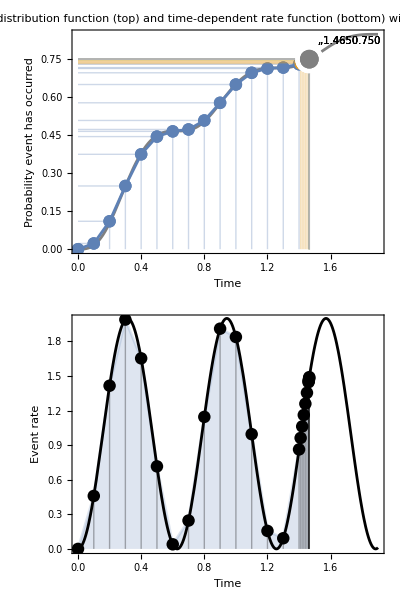

/Users/mishakummel/Documents/2023-24 Academic Year/rotation/review paper/paper figures/appendix.png

```mathematica
appendix=Grid[{{plot1},{plot2}}]
(*Export["FILEPATH/appendix.png",appendix]*)
```